```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
Dim=2;
nsamples=5;
```

```mathematica
ρ=0;
SIGMA={{2^2,ρ},{ρ,(.2)^2}};
```

```mathematica
logprob[x_,y_]=N[-1/2 Simplify[{x,y}.LinearSolve[SIGMA,{x,y}]]];
gentropy[logstd_]:=1/2 Dim(1+Log[2π])+Total[logstd];
vo[params_]:=Module[{mean=params[[;;Dim]],logstd=params[[Dim+1;;]],samples},samples=RandomVariate[NormalDistribution[],{nsamples,Dim}] Transpose[{Table[1,nsamples]}].{Exp[logstd]}+Transpose[{Table[1,nsamples]}].{mean};-Mean[Map[Apply[logprob,#]&,samples]]-gentropy[logstd]]
```

```mathematica
dU[a_,b_,c_,d_]:=GradientG[vo[{a,b,c,d}],{a,b,c,d}];
```

```mathematica
dU1[x_,y_,z_,z1_]:=dU[a,b,c,d]/.{a->x,b->y,c->z,d->z1}
```

```mathematica
dU1[1,2,3,4]
```

{-3.22682,-1063.24,77.5819,74285.9}

```mathematica
adam[grad_,x0_]:=Module[{numiters=10000,stepsize=0.001,b1=0.9,b2=0.999,eps=10^-8,x=x0,m,v,xs=List[]},
m=Table[0,Length[x]];v=Table[0,Length[x]];
For[i=1,i≤numiters,i++,g=Apply[grad,x];m=(1-b1) g+b1 m;
v=(1-b2) g^2+b2 v;
mhat=m/(1-b1^(i+1));
vhat=v/(1-b2^(i+1));
x=x-stepsize mhat/(√vhat+eps);xs=Append[xs,x]];
xs]
```

```mathematica
QS1=RandomVariate[NormalDistribution[],{10000,2}].MatrixPower[SIGMA,.5];
```

```mathematica
xs=adam[dU1,RandomVariate[NormalDistribution[],4]];
```

General::munfl: 0.9^6724 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.9^6725 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.9^6726 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

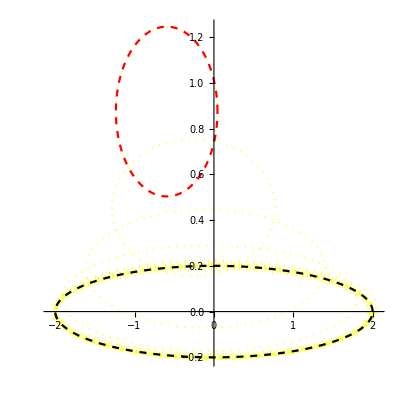

```mathematica
Show[ParametricPlot[Map[(#[[1;;2]]+{Cos[t],Sin[t]}Exp[#[[3;;4]]])&,xs[[1;;Length[xs];;Round[Length[xs]/20]]]],{t,0,2 Pi},PlotStyle->Directive[Red,Dotted,Opacity[1],Yellow],PlotRange->All,AspectRatio->1],ParametricPlot[Map[(#[[1;;2]]+{Cos[t],Sin[t]}Exp[#[[3;;4]]])&,xs[[1;;1]]],{t,0,2 Pi},PlotStyle->Directive[Opacity[1],Dashed,Red],PlotRange->All],ParametricPlot[{Cos[t],Sin[t]}.MatrixPower[SIGMA,.5],{t,0,2 Pi},PlotStyle->Directive[Dashed,Black],PlotRange->All]]
```